# CEE 598: Constitutive Modeling of Engineering Materials HW Assignment 3 -- Bhavesh Shrimali | NetID: bshrima2 | Problem 2

Evolution Equations in the Laplace Domain:

##### Note: A1 and A2 are the transformed functions, in the Laplace domain, of α1 and α2 respectively. This calculation is done by hand a priori

```mathematica
Clear[F]
eveqn1=-2 μ2 * (R F'[R]+F[R] - (R^2 * A1 +A2)) - λ2*(R * F'[R]+3F[R]-(R^2 * A1 + 3*A2)) + 2*ηK * (R^2*s*A1+s*A2)+(ηJ-2/3*ηK)*(R^2 * s*A1 + 3*s*A2);
eveqn2=-2*μ2*(F[R]-A2)-λ2*(R*F'[R]+3*F[R]-(R^2*A1 + 3*A2))+2*ηK*s*A2 + (ηJ - 2/3*ηK)*(R^2*s*A1+3*s*A2);
eveqn1=FullSimplify[eveqn1];
eveqn2=FullSimplify[eveqn2];
soln=Solve[eveqn1==0 && eveqn2==0,{A1,A2}];
A1=A1/.soln;
A2=A2/.soln;
```

#### “Display the Evolution Equations: ”

```mathematica
Chop[eveqn1]
Chop[eveqn2]
```

{-(3 λ2+2 μ2) F[R]-R (λ2+2 μ2) F'[R]+(R μ2 (3 s ηJ+4 s ηK+3 λ2+6 μ2) F'[R])/(3 (s ηK+μ2))-(-9 s ηK λ2 F[R]-6 s ηK μ2 F[R]-9 λ2 μ2 F[R]-6 μ2^2 F[R]-3 R s ηK λ2 F'[R]+3 R s ηJ μ2 F'[R]-2 R s ηK μ2 F'[R])/(3 (s ηK+μ2))}
 |  |  |  |

{-(3 λ2+2 μ2) F[R]-R λ2 F'[R]+(R (3 s ηJ-2 s ηK+3 λ2) μ2 F'[R])/(3 (s ηK+μ2))-(-9 s ηK λ2 F[R]-6 s ηK μ2 F[R]-9 λ2 μ2 F[R]-6 μ2^2 F[R]-3 R s ηK λ2 F'[R]+3 R s ηJ μ2 F'[R]-2 R s ηK μ2 F'[R])/(3 (s ηK+μ2))}
 |  |  |  |

Defining the Principal Stresses in the Laplace Domain:

```mathematica
σ1 = (2μ1 + 2μ2 + λ1+λ2)R F'[R] + (2μ1 + 2μ2 + 3 λ1+3 λ2) F[R] - R^2 (2 μ2 + λ2) A1-(2 μ2 + 3 λ2) A2;
σ2=(λ1 + λ2) R F'[R] + (2  μ1 + 2  μ2  + 3  λ1 + 3 λ2) F[R] - R^2 * λ2 * A1 - (2μ2 + 3  λ2) A2;
```

#### “Display the Principal Stresses”

```mathematica
Chop[FullSimplify[σ1]]
Chop[FullSimplify[σ2]
```

{(3 λ1+3 λ2+2 (μ1+μ2)) F[R]-(R μ2 (λ2+2 μ2) F'[R])/(s ηK+μ2)+R (λ1+λ2+2 (μ1+μ2)) F'[R]-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[R]+R s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[R]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

BLM (in Laplace Domain):

```mathematica
Clear[blm];
blm=D[σ1,R]+2/R*(σ1 - σ2);
blm=FullSimplify[blm];
```

#### “Display the equation of BLM”

```mathematica
Chop[BLM]
```

BLM

Boundary Conditions (in Laplace Domain) :

```mathematica
Clear[bc1];
Clear[bc2];
Clear[Pt];
Pt=Piecewise[{{P0*t,t<=10},{0,t > 10}}];
PL=LaplaceTransform[Pt,t,s];
bc1=PL+σ1/.{R-> A};
bc2=σ1/.{R-> B};
```

#### “Display the Boundary Conditions: ”

```mathematica
Chop[FullSimplify[bc1]]
Chop[FullSimplify[bc2]]
```

{(ⅇ^(-10 s) P0 (-1+ⅇ^(10 s)-10 s))/s^2+(3 λ1+3 λ2+2 (μ1+μ2)) F[A]-(A μ2 (λ2+2 μ2) F'[A])/(s ηK+μ2)+A (λ1+λ2+2 (μ1+μ2)) F'[A]-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[A]+A s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[A]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

{(3 λ1+3 λ2+2 (μ1+μ2)) F[B]-(B μ2 (λ2+2 μ2) F'[B])/(s ηK+μ2)+B (λ1+λ2+2 (μ1+μ2)) F'[B]-((3 λ2+2 μ2) (3 (s ηK+μ2) (3 λ2+2 μ2) F[B]+B s (3 ηK λ2-3 ηJ μ2+2 ηK μ2) F'[B]))/(3 (s ηK+μ2) (3 s ηJ+3 λ2+2 μ2))}
 |  |  |  |

Solving for the Function in the Laplace Domain:

```mathematica
solF=DSolve[{blm=={0},bc1==0,bc2==0},F[R],R];
G2=F[R]/.solF;
P2=InverseLaplaceTransform[G2,s,t];
```

Substitution of the Material Parameters:

```mathematica
μ1 = 1;μ2 = 0.02; κ1 = 100; κ2=50;ηK=2;ηJ=200;
λ1=κ1-2/3 μ1 ; λ2= κ2-2/3 μ2; A=0.001;B=0.01;P0=1;ω=0.1;
```

Plotting the Results :

##### “ Plot of the Radial Displacement u(A)”

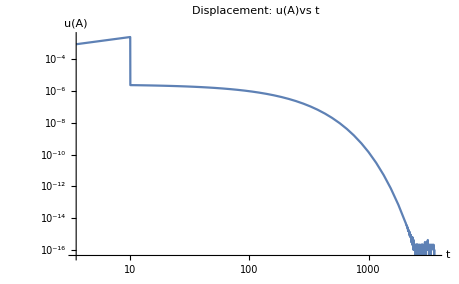

```mathematica
LogLogPlot[A*P2/.{R-> A},{t,0,3600},PlotRange->Automatic,PlotLabel->"Displacement: u(A)vs t",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"t","u(A)"}]
```

##### “ Plot of the Maximum Principle Strain Rf’(A)+f(A) ”

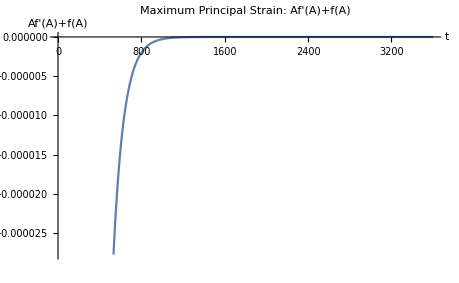

```mathematica
Plot[{R*D[P2,R]+P2}/.{R-> A},{t,0,3600},PlotRange->Automatic,PlotLabel->"Maximum Principal Strain: Af'(A)+f(A)",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"t","Af'(A)+f(A)"}]
```

##### “Plot of the Radial Displacement for t=20 s to observe the discontinuity:”

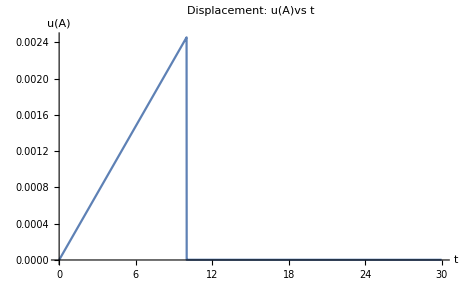

```mathematica
Plot[A*P2/.{R-> A},{t,0,30},PlotRange->Automatic,PlotLabel->"Displacement: u(A)vs t",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"t","u(A)"}]
```

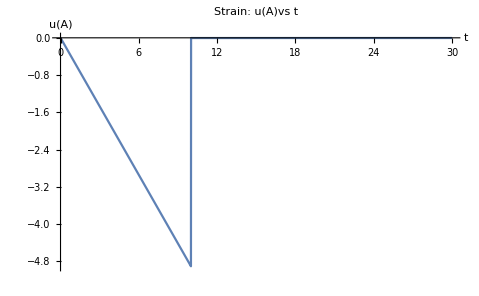

```mathematica
Plot[{R*D[P2,R]+P2}/.{R-> A},{t,0,30},PlotRange->Automatic,PlotLabel->"Strain: u(A)vs t",LabelStyle-> {14,GrayLevel[0]} ,AxesLabel->{"t","u(A)"}]
```